Pesticide model script

```mathematica
Clear["Global`*"]
```

```mathematica
Adot = r*A-α*A*L-f*A
```

-A f+A r-A L α

```mathematica
Ldot = -c*L+β*A*L-f*L
```

-c L-f L+A L β

```mathematica
Solve[{Adot==0,Ldot==0},{A,L}]
```

{{A→(c+f)/β,L→(-f+r)/α},{A→0,L→0}}

```mathematica
eq = Solve[{Adot/A==0,Ldot/L==0},{A,L}]
```

{{A→(c+f)/β,L→(-f+r)/α}}

```mathematica
Aeq=A/.eq;
Leq=L/.eq;
```

```mathematica
jacobian = D[{Adot,Ldot},{{A,L}}]
```

{{-f+r-L α,-A α},{L β,-c-f+A β}}

```mathematica
MatrixForm[jacobian]
```

(-f+r-L α | -A α
L β | -c-f+A β)

```mathematica
r=0.21;
α=0.13;
c=0.10;
β=0.08;
k=3;
```

```mathematica
Manipulate[Eigenvalues[D[{r*A-α*A*L-f*A,-c*L+β*A*L-f*L},{{A,L}}]]/.{A->(c+f)/β,L->(-f+r)/α},{f,0,0.1}]
```

```mathematica
Manipulate[StreamPlot[{r*A-α*A*L-f*A,-c*L+β*A*L-f*L},{A,-0.25,10},{L,-0.25,10},Axes->True],{f,0,0.1}]
```

```mathematica
Simplify[Reduce[(-c*L+β*A*L-f*A≤0),f],f∈Reals]
```

(A==0&&L≥0)||(A<0&&f≤(0.08-0.1/A) L)||(A>0&&f≥(0.08-0.1/A) L)

```mathematica
f=0.1;
```

```mathematica
Eigenvalues[jacobian]/.{A->Aeq,L->Leq}
```

{{8.88178×10^-18-0.148324 ⅈ},{8.88178×10^-18+0.148324 ⅈ}}

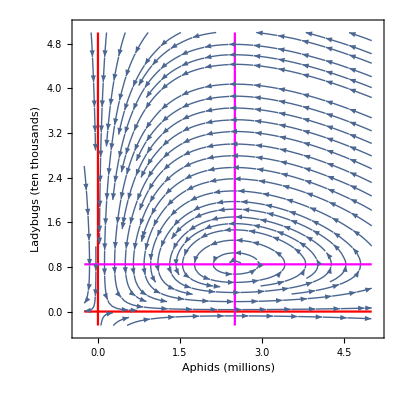

```mathematica
Show[
StreamPlot[{r*A-α*A*L-f*A,-c*L+β*A*L-f*L},{A,-0.25,5},{L,-0.25,5},Axes->True,AxesLabel->{"A","L"},FrameLabel->{"Aphids (millions)","Ladybugs (ten thousands)"},Frame->True,LabelStyle->{Black,30},ImageSize->Full],
ContourPlot[{A==0,L==0,A==Aeq,L==Leq},{A,-0.25,5},{L,-0.25,5},ContourStyle->{Red,Red,Magenta,Magenta} ]
]
```

```mathematica
Aeq
```

{2.5}

```mathematica
Leq
```

{0.846154}